```mathematica
Quit
```

# Formatting of axes part 1- Plot 2D

```mathematica
f[x_]:=x^2;
```

```mathematica
Plot
```

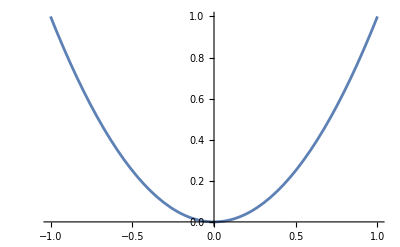

```mathematica
Plot[f[x],{x,-1,1}]
```

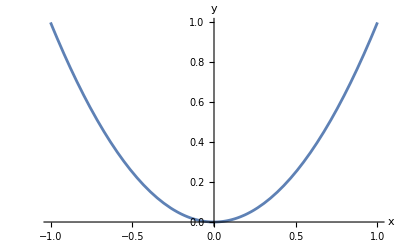

```mathematica
Plot[f[x],{x,-1,1},AxesLabel->{"x","y"}]
```

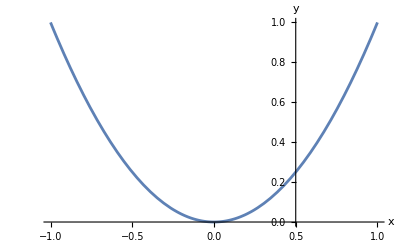

```mathematica
Plot[f[x],{x,-1,1},AxesLabel->{"x","y"},AxesOrigin->{0.5,0}]
```

```mathematica
Plot[f[x],{x,-1,1},AxesLabel->{"x","y"},AxesLabel->{"x","y"},AxesStyle->Directive[Orange,12]]
```

-Graphics-

```mathematica
Plot[f[x],{x,-1,1},AxesLabel->{"x","y"},AxesLabel->{"x","y"},AxesStyle->{Directive[Orange,12],Directive[Green,8]}]
```

-Graphics-

```mathematica
Plot[f[x],{x,-1,1},Axes->{True,False}]
```

-Graphics-

```mathematica
Plot[f[x],{x,-1,1},Axes->{False,True}]
```

-Graphics-

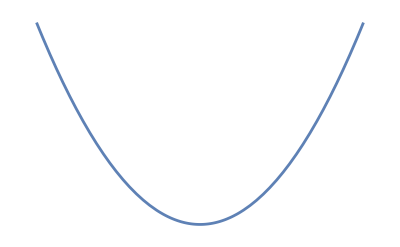

```mathematica
Plot[f[x],{x,-1,1},Axes->{False,False}]
```